Use Block to provide a scope in which local parameters can be isolated from outside. You can make proper assumptions on the local parameters so that the problems can be handled more smoothly.

```mathematica
asol=Block[{k,a0,νA,deq,$Assumptions=k>0&&a0>0&&νA>0},
SetAttributes[{k,a0,νA},Constant];
deq=-D[a[t],t]/νA==k a[t];
DSolve[deq&&a[0]==a0,a[t],t]
]
```

{{a[t]→a0 ⅇ^(-k t νA)}}

Using another Block, one can give numerical values to parameters locally, without worrying about affecting the global parameters possibly having the same names.

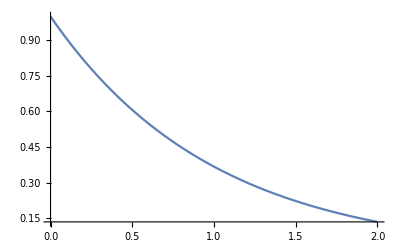

```mathematica
Block[{k=1,a0=1,νA=1},
Plot[a[t]/.asol[[1]],{t,0,2}]
]
```

Try to make the figure fancier by yourself.